```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
<<Format`
(*<<Optimize`*)
```

```mathematica
(* Start with expansions of 5th order *)
F :=F0+F1 x/dx + F2 x^2/2/dx^2+F3 x^3/6/dx^3+F4 x^4/24/dx^4;
f:=f0+f1 x/dx + f2 x^2/2/dx^2+f3 x^3/6/dx^3+f4 x^4/24/dx^4;
(* We are given the "average" value F0 at x = 0, we want to find the "point" value f0.
For this, construct the running average of f which by definition equals F *)
RunningAverage:=Integrate[f,{x,t-dx/2,t+dx/2}]/dx; (* == F by def. *)
(* Equate F and RunningAverage and determine the coefficients, f# *)
Collect[FullSimplify[RunningAverage],t]
sol=Solve[CoefficientList[RunningAverage,t] ==CoefficientList[F,x],{f0,f1,f2,f3,f4}]
```

(80 (24 f0+f2)+f4)/1920+((24 f1+f3) t)/(24 dx)+((24 f2+f4) t^2)/(48 dx^2)+(f3 t^3)/(6 dx^3)+(f4 t^4)/(24 dx^4)

{{f0→(5760 F0-240 F2+7 F4)/5760,f1→1/24 (24 F1-F3),f2→1/24 (24 F2-F4),f3→F3,f4→F4}}

```mathematica
a2cF=Collect[FullSimplify[f//.sol[[1]]],x]
```

(5760 F0-240 F2+7 F4)/5760+((24 F1-F3) x)/(24 dx)+((24 F2-F4) x^2)/(48 dx^2)+(F3 x^3)/(6 dx^3)+(F4 x^4)/(24 dx^4)

```mathematica
RunningAverage//.{f5->0,dx->1}
```

f0+f2/24+f4/1920+f1 t+(f3 t)/24+(f2 t^2)/2+(f4 t^2)/48+(f3 t^3)/6+(f4 t^4)/24

```mathematica
FullSimplify[(a2cF//.{x->+dx/2})-(a2cF//.{x->-dx/2})]
```

F1

```mathematica
(* The desired point value f0 is *)
PointValue=f0/.sol
```

{(5760 F0-240 F2+7 F4)/5760}

```mathematica
(* start rest-mass flux *)
```

```mathematica
gdetpre=gdet0+gdet1*x/dx+gdet2*x^2/dx^2;
rhopre:=rho0+rho1 x/dx + rho2/dx^2 x^2;
udirpre:=udir0+udir1/dx x + udir2/dx^2 x^2;
```

```mathematica
(* Specifically, we want to feed in 3 densities, 3 velocities, 3 gdets, and get back flux correction at 2 faces *)

eq1gdet=gdetl==gdetpre//.{x->-dx/2};
eq2gdet=gdetc==gdetpre//.{x->0};
eq3gdet=gdetr==gdetpre//.{x->dx/2};
solgdet=Solve[{eq1gdet,eq2gdet,eq3gdet},{gdet0,gdet1,gdet2}][[1]];
gdet=gdetpre//.solgdet

eq1rho=rhol==rhopre//.{x->-dx/2};
eq2rho=rhoc==rhopre//.{x->0};
eq3rho=rhor==rhopre//.{x->dx/2};
solrho=Solve[{eq1rho,eq2rho,eq3rho},{rho0,rho1,rho2}][[1]];
rho=rhopre//.solrho

eq1udir=udirl==udirpre//.{x->-dx/2};
eq2udir=udirc==udirpre//.{x->0};
eq3udir=udirr==udirpre//.{x->dx/2};
soludir=Solve[{eq1udir,eq2udir,eq3udir},{udir0,udir1,udir2}][[1]];
udir=udirpre//.soludir
```

gdetc+((-gdetl+gdetr) x)/dx-(2 (2 gdetc-gdetl-gdetr) x^2)/dx^2

rhoc+((-rhol+rhor) x)/dx-(2 (2 rhoc-rhol-rhor) x^2)/dx^2

udirc+((-udirl+udirr) x)/dx-(2 (2 udirc-udirl-udirr) x^2)/dx^2

```mathematica
(* setup flux and a2c of flux in raw form *)
F=gdet*rho*udir;
f:=f0+f1 x/dx + f2/dx^2 x^2+f3/dx^3 x^3+f4/dx^4 x^4+f5/dx^5 x^5+f6/dx^6 x^6;
```

```mathematica
RunningAverage:=Integrate[f,{x,t-dx/2,t+dx/2}]/dx;
solf=Solve[CoefficientList[RunningAverage,t] ==CoefficientList[F,x],{f0,f1,f2,f3,f4,f5,f6}]
ffinal=FullSimplify[f//.solf[[1]]]
```

{{f0→1/210 (1024 gdetc rhoc udirc-288 gdetl rhoc udirc-288 gdetr rhoc udirc-288 gdetc rhol udirc+60 gdetl rhol udirc+144 gdetr rhol udirc-288 gdetc rhor udirc+144 gdetl rhor udirc+60 gdetr rhor udirc-288 gdetc rhoc udirl+60 gdetl rhoc udirl+144 gdetr rhoc udirl+60 gdetc rhol udirl-2 gdetl rhol udirl-51 gdetr rhol udirl+144 gdetc rhor udirl-51 gdetl rhor udirl-51 gdetr rhor udirl-288 gdetc rhoc udirr+144 gdetl rhoc udirr+60 gdetr rhoc udirr+144 gdetc rhol udirr-51 gdetl rhol udirr-51 gdetr rhol udirr+60 gdetc rhor udirr-51 gdetl rhor udirr-2 gdetr rhor udirr),f1→1/6 (-32 gdetl rhoc udirc+32 gdetr rhoc udirc-32 gdetc rhol udirc+20 gdetl rhol udirc+32 gdetc rhor udirc-20 gdetr rhor udirc-32 gdetc rhoc udirl+20 gdetl rhoc udirl+20 gdetc rhol udirl-9 gdetl rhol udirl-5 gdetr rhol udirl-5 gdetl rhor udirl+5 gdetr rhor udirl+32 gdetc rhoc udirr-20 gdetr rhoc udirr-5 gdetl rhol udirr+5 gdetr rhol udirr-20 gdetc rhor udirr+5 gdetl rhor udirr+9 gdetr rhor udirr),f2→1/2 (-128 gdetc rhoc udirc+48 gdetl rhoc udirc+48 gdetr rhoc udirc+48 gdetc rhol udirc-12 gdetl rhol udirc-24 gdetr rhol udirc+48 gdetc rhor udirc-24 gdetl rhor udirc-12 gdetr rhor udirc+48 gdetc rhoc udirl-12 gdetl rhoc udirl-24 gdetr rhoc udirl-12 gdetc rhol udirl+gdetl rhol udirl+9 gdetr rhol udirl-24 gdetc rhor udirl+9 gdetl rhor udirl+9 gdetr rhor udirl+48 gdetc rhoc udirr-24 gdetl rhoc udirr-12 gdetr rhoc udirr-24 gdetc rhol udirr+9 gdetl rhol udirr+9 gdetr rhol udirr-12 gdetc rhor udirr+9 gdetl rhor udirr+gdetr rhor udirr),f3→1/3 (64 gdetl rhoc udirc-64 gdetr rhoc udirc+64 gdetc rhol udirc-52 gdetl rhol udirc-64 gdetc rhor udirc+52 gdetr rhor udirc+64 gdetc rhoc udirl-52 gdetl rhoc udirl-52 gdetc rhol udirl+27 gdetl rhol udirl+13 gdetr rhol udirl+13 gdetl rhor udirl-13 gdetr rhor udirl-64 gdetc rhoc udirr+52 gdetr rhoc udirr+13 gdetl rhol udirr-13 gdetr rhol udirr+52 gdetc rhor udirr-13 gdetl rhor udirr-27 gdetr rhor udirr),f4→4 (32 gdetc rhoc udirc-14 gdetl rhoc udirc-14 gdetr rhoc udirc-14 gdetc rhol udirc+5 gdetl rhol udirc+7 gdetr rhol udirc-14 gdetc rhor udirc+7 gdetl rhor udirc+5 gdetr rhor udirc-14 gdetc rhoc udirl+5 gdetl rhoc udirl+7 gdetr rhoc udirl+5 gdetc rhol udirl-gdetl rhol udirl-3 gdetr rhol udirl+7 gdetc rhor udirl-3 gdetl rhor udirl-3 gdetr rhor udirl-14 gdetc rhoc udirr+7 gdetl rhoc udirr+5 gdetr rhoc udirr+7 gdetc rhol udirr-3 gdetl rhol udirr-3 gdetr rhol udirr+5 gdetc rhor udirr-3 gdetl rhor udirr-gdetr rhor udirr),f5→-4 (4 gdetl rhoc udirc-4 gdetr rhoc udirc+4 gdetc rhol udirc-4 gdetl rhol udirc-4 gdetc rhor udirc+4 gdetr rhor udirc+4 gdetc rhoc udirl-4 gdetl rhoc udirl-4 gdetc rhol udirl+3 gdetl rhol udirl+gdetr rhol udirl+gdetl rhor udirl-gdetr rhor udirl-4 gdetc rhoc udirr+4 gdetr rhoc udirr+gdetl rhol udirr-gdetr rhol udirr+4 gdetc rhor udirr-gdetl rhor udirr-3 gdetr rhor udirr),f6→-8 (8 gdetc rhoc udirc-4 gdetl rhoc udirc-4 gdetr rhoc udirc-4 gdetc rhol udirc+2 gdetl rhol udirc+2 gdetr rhol udirc-4 gdetc rhor udirc+2 gdetl rhor udirc+2 gdetr rhor udirc-4 gdetc rhoc udirl+2 gdetl rhoc udirl+2 gdetr rhoc udirl+2 gdetc rhol udirl-gdetl rhol udirl-gdetr rhol udirl+2 gdetc rhor udirl-gdetl rhor udirl-gdetr rhor udirl-4 gdetc rhoc udirr+2 gdetl rhoc udirr+2 gdetr rhoc udirr+2 gdetc rhol udirr-gdetl rhol udirr-gdetr rhol udirr+2 gdetc rhor udirr-gdetl rhor udirr-gdetr rhor udirr)}}

1/(210 dx^6)(dx^6 (gdetl (60 rhol udirc+144 rhor udirc-2 rhol udirl-51 rhor udirl-51 (rhol+rhor) udirr+12 rhoc (-24 udirc+5 udirl+12 udirr))+gdetr (rhor (60 udirc-51 udirl-2 udirr)+12 rhoc (-24 udirc+12 udirl+5 udirr)+3 rhol (48 udirc-17 (udirl+udirr)))+4 gdetc (3 rhor (-24 udirc+12 udirl+5 udirr)+3 rhol (-24 udirc+5 udirl+12 udirr)+8 rhoc (32 udirc-9 (udirl+udirr))))-35 dx^5 (gdetr (-32 rhoc udirc+20 rhor udirc+5 rhol udirl-5 rhor udirl+20 rhoc udirr-5 rhol udirr-9 rhor udirr)+4 gdetc (8 rhol udirc-8 rhor udirc+8 rhoc udirl-5 rhol udirl-8 rhoc udirr+5 rhor udirr)+gdetl (4 rhoc (8 udirc-5 udirl)+5 rhor (udirl-udirr)+rhol (-20 udirc+9 udirl+5 udirr))) x-105 dx^4 (-gdetr (12 rhoc (4 udirc-2 udirl-udirr)+rhor (-12 udirc+9 udirl+udirr)+3 rhol (-8 udirc+3 (udirl+udirr)))-gdetl (12 rhoc (4 udirc-udirl-2 udirr)+rhol (-12 udirc+udirl+9 udirr)+3 rhor (-8 udirc+3 (udirl+udirr)))+4 gdetc (4 rhoc (8 udirc-3 (udirl+udirr))+3 (rhor (-4 udirc+2 udirl+udirr)+rhol (-4 udirc+udirl+2 udirr)))) x^2+70 dx^3 (gdetl (64 rhoc udirc-52 rhol udirc-52 rhoc udirl+27 rhol udirl+13 rhor udirl+13 (rhol-rhor) udirr)+4 gdetc (16 rhol udirc-16 rhor udirc-13 rhol udirl+16 rhoc (udirl-udirr)+13 rhor udirr)+gdetr (rhor (52 udirc-13 udirl-27 udirr)+13 rhol (udirl-udirr)+rhoc (-64 udirc+52 udirr))) x^3+840 dx^2 (gdetc (rhor (-14 udirc+7 udirl+5 udirr)+rhol (-14 udirc+5 udirl+7 udirr)+2 rhoc (16 udirc-7 (udirl+udirr)))-gdetr (rhoc (14 udirc-7 udirl-5 udirr)+rhor (-5 udirc+3 udirl+udirr)+rhol (-7 udirc+3 (udirl+udirr)))-gdetl (rhoc (14 udirc-5 udirl-7 udirr)+rhol (-5 udirc+udirl+3 udirr)+rhor (-7 udirc+3 (udirl+udirr)))) x^4-840 dx (4 gdetc (rhol (udirc-udirl)+rhoc (udirl-udirr)+rhor (-udirc+udirr))+gdetl (4 rhoc (udirc-udirl)+rhor (udirl-udirr)+rhol (-4 udirc+3 udirl+udirr))-gdetr (4 rhoc (udirc-udirr)+rhol (-udirl+udirr)+rhor (-4 udirc+udirl+3 udirr))) x^5-1680 (2 gdetc-gdetl-gdetr) (2 rhoc-rhol-rhor) (2 udirc-udirl-udirr) x^6)

```mathematica
(* Now get what really want, which is correction to 0th order flux at face *)
```

```mathematica
(* the flux correction at x=-dx/2 *)
where=-dx/2;
fl=ffinal//.{x->where};
Fl=F//.(x->where);
leftcorr=FullSimplify[fl-Fl]
(*CForm[N[leftcorr,32]]*)
CAssign[Fleft,leftcorr,AssignOptimize->True,OptimizePower->Binary,OptimizePlus->True,OptimizeCoefficients->True,AssignPrecision->32,AssignMaxSize->200]
```

1/210 (gdetc (-866 rhoc udirc+447 rhol udirc+237 rhor udirc+447 rhoc udirl-45 rhol udirl-171 rhor udirl+3 (79 rhoc-57 rhol-15 rhor) udirr)+gdetr (3 rhoc (79 udirc-57 udirl-15 udirr)+rhor (-45 udirc+54 udirl-2 udirr)+9 rhol (-19 udirc+6 (udirl+udirr)))+gdetl (3 rhoc (149 udirc-15 udirl-57 udirr)+rhol (-45 udirc-212 udirl+54 udirr)+9 rhor (-19 udirc+6 (udirl+udirr))))

Internal_$$59479=-45.*udirc;
Internal_$$59484=-19.*udirc;
Internal_$$59485=udirl+udirr;
Internal_$$59486=6.*Internal_$$59485;
Internal_$$59487=Internal_$$59484+Internal_$$59486;
t[1]=-866.*rhoc*udirc;
t[2]=447.*rhol*udirc;
t[3]=237.*rhor*udirc;
t[4]=447.*rhoc*udirl;
t[5]=-45.*rhol*udirl;
t[6]=-171.*rhor*udirl;
t[7]=79.*rhoc;
t[8]=-57.*rhol;
t[9]=-15.*rhor;
t[10]=udirr*(t[7]+t[8]+t[9]);
t[11]=t[6];
t[12]=3.*t[10];
t[13]=t[1]+t[2]+t[3];
t[14]=t[4]+t[5]+t[11]+t[12];
t[15]=79.*udirc;
t[16]=-57.*udirl;
t[17]=-15.*udirr;
t[18]=rhoc*(t[15]+t[16]+t[17]);
t[19]=54.*udirl;
t[20]=-2.*udirr+Internal_$$59479;
t[21]=9.*rhol*Internal_$$59487;
t[22]=rhor*(t[19]+t[20]);
t[23]=t[21];
t[24]=3.*t[18];
t[25]=t[22]+t[23];
t[26]=149.*udirc;
t[27]=-15.*udirl;
t[28]=-57.*udirr;
t[29]=rhoc*(t[26]+t[27]+t[28]);
t[30]=-212.*udirl;
t[31]=54.*udirr+Internal_$$59479;
t[32]=9.*rhor*Internal_$$59487;
t[33]=rhol*(t[30]+t[31]);
t[34]=t[32];
t[35]=3.*t[29];
t[36]=t[33]+t[34];
t[37]=gdetr*(t[24]+t[25]);
t[38]=gdetl*(t[35]+t[36]);
t[39]=gdetc*(t[13]+t[14]);
t[40]=t[37]+t[38];
t[41]=t[39]+t[40];
Fleft=0.0047619047619047619047619047619048*t[41];

```mathematica
(*
constsdeath={gdetl->0.5,gdetc->0.5,gdetr->0.5,rhol->-7.35287*10^(-18), rhoc->-9.76538*10^(-14), rhor->-1.95286*10^(-13),udirl->-2.94115*10^(-17), udirc->-3.90615*10^(-13), udirr->-7.81142*10^(-13)}
*)
```

```mathematica
constsdeath={gdetl->0.5,gdetc->0.5,gdetr->0.5,rhol->-7.35287*10^(-18), rhoc->-9.76538*10^(-14), rhor->-1.95286*10^(-13),udirl->-2.94115*10^(-50), udirc->-3.90615*10^(-13), udirr->-7.81142*10^(-13)}
```

{gdetl→0.5,gdetc→0.5,gdetr→0.5,rhol→-7.35287×10^-18,rhoc→-9.76538×10^-14,rhor→-1.95286×10^-13,udirl→-2.94115×10^-50,udirc→-3.90615×10^-13,udirr→-7.81142×10^-13}

```mathematica
Fl//.constsdeath
fl//.constsdeath
leftcorr//.constsdeath
(gdetl*1*udirl*rhol+10^(-30))//.constsdeath
```

0.

-6.35821×10^-27

-6.35821×10^-27

1.×10^-30

```mathematica
myF=F//.constsdeath//.{dx->1}
myf=ffinal//.constsdeath//.{dx->1}
```

(0.5+0. x+0. x^2) (-9.76538×10^-14-1.95279×10^-13 x+2.84943×10^-17 x^2) (-3.90615×10^-13-7.81142×10^-13 x+1.76×10^-16 x^2)

1/210 (2.67075×10^-24+1.60203×10^-23 x+1.60138×10^-23 x^2-5.94585×10^-27 x^3+5.26574×10^-31 x^4-1.07539×10^-38 x^5+0. x^6)

```mathematica
myF//.{x->0}
myf//.{x->0}
```

1.90725×10^-26

1.27179×10^-26

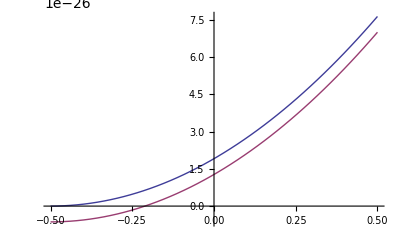

```mathematica
Plot[{myF,myf},{x,-1/2,1/2}]
```

```mathematica
(* the flux correction at x=+dx/2 *)
where=dx/2;
fr=ffinal//.{x->where};
Fr=F//.(x->where);
rightcorr=FullSimplify[fr-Fr]
(*CForm[N[rightcorr,32]]*)
CAssign[Fright,rightcorr,AssignOptimize->True,OptimizePower->Binary,OptimizePlus->True,OptimizeCoefficients->True,AssignPrecision->32,AssignMaxSize->200]
```

1/210 (gdetc (3 (rhol (79 udirc-15 udirl-57 udirr)+rhor (149 udirc-57 udirl-15 udirr))+rhoc (-866 udirc+237 udirl+447 udirr))+gdetr (rhor (-45 udirc+54 udirl-212 udirr)+3 rhoc (149 udirc-57 udirl-15 udirr)+9 rhol (-19 udirc+6 (udirl+udirr)))+gdetl (3 rhoc (79 udirc-15 udirl-57 udirr)+rhol (-45 udirc-2 udirl+54 udirr)+9 rhor (-19 udirc+6 (udirl+udirr))))

Internal_$$59365=149.*udirc;
Internal_$$59366=-57.*udirl;
Internal_$$59367=-15.*udirr;
Internal_$$59368=Internal_$$59365+Internal_$$59366+Internal_$$59367;
Internal_$$59360=79.*udirc;
Internal_$$59361=-15.*udirl;
Internal_$$59362=-57.*udirr;
Internal_$$59363=Internal_$$59360+Internal_$$59361+Internal_$$59362;
Internal_$$59379=-45.*udirc;
Internal_$$59385=-19.*udirc;
Internal_$$59386=udirl+udirr;
Internal_$$59387=6.*Internal_$$59386;
Internal_$$59388=Internal_$$59385+Internal_$$59387;
t[1]=-866.*udirc;
t[2]=237.*udirl;
t[3]=447.*udirr;
t[4]=rhol*Internal_$$59363+rhor*Internal_$$59368;
t[5]=rhoc*(t[1]+t[2]+t[3]);
t[6]=3.*t[4];
t[7]=3.*rhoc*Internal_$$59368;
t[8]=54.*udirl;
t[9]=-212.*udirr+Internal_$$59379;
t[10]=9.*rhol*Internal_$$59388;
t[11]=rhor*(t[8]+t[9]);
t[12]=t[10];
t[13]=3.*rhoc*Internal_$$59363;
t[14]=-2.*udirl;
t[15]=54.*udirr+Internal_$$59379;
t[16]=9.*rhor*Internal_$$59388;
t[17]=rhol*(t[14]+t[15]);
t[18]=t[16];
t[19]=gdetr*(t[7]+t[11]+t[12]);
t[20]=gdetl*(t[13]+t[17]+t[18]);
t[21]=gdetc*(t[5]+t[6]);
t[22]=t[19]+t[20];
t[23]=t[21]+t[22];
Fright=0.0047619047619047619047619047619048*t[23];

```mathematica
Fr//.constsdeath
fr//.constsdeath
rightcorr//.constsdeath
(gdetr*1*udirr*rhor+10^(-30))//.constsdeath
```

7.6273×10^-26

6.99219×10^-26

-6.35113×10^-27

7.6274×10^-26

```mathematica
(* check what flux difference resolves to *)
difff=FullSimplify[(fr-fl)/dx]
(* compare with expected result *)
dFdx=D[F,x]//.{x->0}
FullSimplify[difff-dFdx]
```

(-gdetl rhoc udirc+gdetr rhoc udirc+gdetc (-rhol udirc+rhor udirc+rhoc (-udirl+udirr)))/dx

((-gdetl+gdetr) rhoc udirc)/dx+(gdetc (-rhol+rhor) udirc)/dx+(gdetc rhoc (-udirl+udirr))/dx

0

```mathematica
(* So agrees as required *)
```